## Nullifiers of a partially entangled state at a given hierarchy level

## Preliminaries

### Qubit space

We want to study the geometry of the quantum set of behaviors (correlations), which is convex. Specifically, we want to study the quantum set through the dual perspective. Since one can fully characterize a convex set in terms of its extremal points, it will be then sufficient to study orthogonal faces (faces of the dual).

One defines operators acting on the single-qubit space as

```mathematica
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
I2=IdentityMatrix[2];
```

and operators acting on the 2-qubit space using the tensor product of single-qubit operators as

```mathematica
ZA=KroneckerProduct[Z,I2];
ZB=KroneckerProduct[I2,Z];
XA=KroneckerProduct[X,I2];
XB=KroneckerProduct[I2,X];
ZZ=KroneckerProduct[Z,Z];
XX=KroneckerProduct[X,X];
ZX=KroneckerProduct[Z,X];
XZ=KroneckerProduct[X,Z];
II=KroneckerProduct[I2,I2];
```

### Non-commuting algebra

```mathematica
ClearAll[nc,Id,A0,A1,B0,B1]
SetAttributes[nc,{Flat,OneIdentity}]
scalarQ[expr_]:=NumericQ[expr]||MatchQ[expr,g[_,_]]||FreeQ[expr,A0|A1|B0|B1|nc|Id];
rules={
(*Squares equal identity*)
nc[A0,A0]:>nc[Id],nc[A1,A1]:>nc[Id],
nc[B0,B0]:>nc[Id],nc[B1,B1]:>nc[Id],
nc[Id,Id]:>nc[Id],

(*Id acts as identity element*)
nc[Id,x_]:>nc[x],nc[x_,Id]:>nc[x],

(*Id commutes with everything*)
nc[a___,Id,b___]:>nc[a,b],

(*A_i and B_j commute*)
nc[a___,A0,B0,b___]:>nc[a,B0,A0,b],
nc[a___,A0,B1,b___]:>nc[a,B1,A0,b],
nc[a___,A1,B0,b___]:>nc[a,B0,A1,b],
nc[a___,A1,B1,b___]:>nc[a,B1,A1,b],

(*Scalars*)
nc[a___,c_?NumericQ,b___]:>c*nc[a,b],
nc[a___,c_?scalarQ,b___]:>c*nc[a,b],

(*Distributive rule*)
nc[a___,x_+y_,b___]:>nc[a,x,b]+nc[a,y,b],
nc[a___,Times[s_?scalarQ,x_],b___]:>s*nc[a,x,b]
};

simplify[expr_]:=FixedPoint[ReplaceAll[#,rules]&,expr];
```

```mathematica
comm[X_,Y_]:=simplify[nc[X,Y]-nc[Y,X]];
```

```mathematica
ncDot[vec1_List,mat_,vec2_List]:=Module[{res},res=Sum[nc[vec1[[i]],mat[[i,j]],vec2[[j]]],{i,Length[vec1]},{j,Length[vec2]}];
simplify[res]]
```

## Tsirelson point

### Τ_(1+A+B+AB+ABB') of the NPA hierarchy

Consider the state

```mathematica
phiPlus:= 1/Sqrt[2]{1,0,0,1};
A[i_]:=(ZA+(-1)^i XA)/Sqrt[2] ;
B[0]=ZB;
B[1]=XB;
```

We want to find a basis of nullifiers for this state, in terms of the following operators (2 level of the NPA ), written in a vector form

```mathematica
(*Here, A and B are non-commutative operators*)
M2nc={nc[Id], nc[A0],nc[A1],nc[B0],nc[B1],nc[A0,B0],nc[A0,B1],nc[A1,B0],nc[A1,B1],nc[A0,B0,B1],nc[A0,B1,B0],nc[A1,B0,B1],nc[A1,B1,B0]};
M2:={II, A[0],A[1],B[0],B[1],A[0].B[0],A[0].B[1],A[1].B[0],A[1].B[1],A[0].B[0].B[1],A[0].B[1].B[0],A[1].B[0].B[1],A[1].B[1].B[0]};
```

Hence, we want to find

```mathematica
v2 = {id,a0,a1,b0,b1,c00,c01,c10, c11,d001,d010,d101,d110};
v2.M2//MatrixForm
```

(a0/(√2)+a1/(√2)+b0+c00/(√2)+c10/(√2)+id | b1+c01/(√2)+c11/(√2)+d001/(√2)-d010/(√2)+d101/(√2)-d110/(√2) | a0/(√2)-a1/(√2)+c00/(√2)-c10/(√2) | c01/(√2)-c11/(√2)+d001/(√2)-d010/(√2)-d101/(√2)+d110/(√2)
b1+c01/(√2)+c11/(√2)-d001/(√2)+d010/(√2)-d101/(√2)+d110/(√2) | a0/(√2)+a1/(√2)-b0-c00/(√2)-c10/(√2)+id | c01/(√2)-c11/(√2)-d001/(√2)+d010/(√2)+d101/(√2)-d110/(√2) | a0/(√2)-a1/(√2)-c00/(√2)+c10/(√2)
a0/(√2)-a1/(√2)+c00/(√2)-c10/(√2) | c01/(√2)-c11/(√2)+d001/(√2)-d010/(√2)-d101/(√2)+d110/(√2) | -a0/(√2)-a1/(√2)+b0-c00/(√2)-c10/(√2)+id | b1-c01/(√2)-c11/(√2)-d001/(√2)+d010/(√2)-d101/(√2)+d110/(√2)
c01/(√2)-c11/(√2)-d001/(√2)+d010/(√2)+d101/(√2)-d110/(√2) | a0/(√2)-a1/(√2)-c00/(√2)+c10/(√2) | b1-c01/(√2)-c11/(√2)+d001/(√2)-d010/(√2)+d101/(√2)-d110/(√2) | -a0/(√2)-a1/(√2)-b0+c00/(√2)+c10/(√2)+id)

Then, we impose the nullifying condition:

```mathematica
eqs=Thread[v2.M2.phiPlus==0]
```

{(c01/(√2)-c11/(√2)+d001/(√2)-d010/(√2)-d101/(√2)+d110/(√2))/(√2)+(a0/(√2)+a1/(√2)+b0+c00/(√2)+c10/(√2)+id)/(√2)==0,(a0/(√2)-a1/(√2)-c00/(√2)+c10/(√2))/(√2)+(b1+c01/(√2)+c11/(√2)-d001/(√2)+d010/(√2)-d101/(√2)+d110/(√2))/(√2)==0,(a0/(√2)-a1/(√2)+c00/(√2)-c10/(√2))/(√2)+(b1-c01/(√2)-c11/(√2)-d001/(√2)+d010/(√2)-d101/(√2)+d110/(√2))/(√2)==0,(c01/(√2)-c11/(√2)-d001/(√2)+d010/(√2)+d101/(√2)-d110/(√2))/(√2)+(-a0/(√2)-a1/(√2)-b0+c00/(√2)+c10/(√2)+id)/(√2)==0}

```mathematica
sol=Solve[eqs, v2]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{id→-√2 c01-√2 c10,b0→-√2 a1+b1-√2 d001+√2 d010,c11→c00-c01-c10,d110→-a0+a1-√2 b1+d001-d010+d101}}

```mathematica
w=v2/.sol[[1]];
w//MatrixForm
```

(-√2 c01-√2 c10
a0
a1
-√2 a1+b1-√2 d001+√2 d010
b1
c00
c01
c10
c00-c01-c10
d001
d010
d101
-a0+a1-√2 b1+d001-d010+d101)

The free parameters are a0, a1, b1, c00, c01, c10, d001, d010, d101

Then, a basis is given by assigning 1 to each coefficient one by one:

```mathematica
w1 = w/.{a0->1,a1->0,b1->0,c00->0,c01->0,c10->0,d001->0,d010->0,d101->0};
w2= w/.{a0->0,a1->1,b1->0,c00->0,c01->0,c10->0,d001->0,d010->0,d101->0};
w3 = w/.{a0->0,a1->0,b1->1,c00->0,c01->0,c10->0,d001->0,d010->0,d101->0};
w4 = w/.{a0->0,a1->0,b1->0,c00->1,c01->0,c10->0,d001->0,d010->0,d101->0};
w5 = w/.{a0->0,a1->0,b1->0,c00->0,c01->1,c10->0,d001->0,d010->0,d101->0};
w6 = w/.{a0->0,a1->0,b1->0,c00->0,c01->0,c10->1,d001->0,d010->0,d101->0};
w7 = w/.{a0->0,a1->0,b1->0,c00->0,c01->0,c10->0,d001->1,d010->0,d101->0};
w8 = w/.{a0->0,a1->0,b1->0,c00->0,c01->0,c10->0,d001->0,d010->1,d101->0};
w9 = w/.{a0->0,a1->0,b1->0,c00->0,c01->0,c10->0,d001->0,d010->0,d101->1};
basis2 = {w1,w2,w3,w4,w5,w6,w7,w8,w9};
basis2 //TableForm
```

0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-√2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0
-√2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -√2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1

```mathematica
MatrixRank[basis2]
```

9

So the vectors are all linear independent!

```mathematica
Nullbasis2nc=basis2.M2nc;
Nullbasis2nc//MatrixForm
```

(nc[A0]-nc[A1,B1,B0]
nc[A1]-√2 nc[B0]+nc[A1,B1,B0]
nc[B0]+nc[B1]-√2 nc[A1,B1,B0]
nc[A0,B0]+nc[A1,B1]
-√2 nc[Id]+nc[A0,B1]-nc[A1,B1]
-√2 nc[Id]+nc[A1,B0]-nc[A1,B1]
-√2 nc[B0]+nc[A0,B0,B1]+nc[A1,B1,B0]
√2 nc[B0]+nc[A0,B1,B0]-nc[A1,B1,B0]
nc[A1,B0,B1]+nc[A1,B1,B0])

Let us first verify that these are nullifiers.

```mathematica
Clear[A,B,II];
Nullbasis2 = basis2.M2;
```

```mathematica
Nullbasis2 //MatrixForm
```

(A[0]-A[1].B[1].B[0]
A[1]-√2 B[0]+A[1].B[1].B[0]
B[0]+B[1]-√2 A[1].B[1].B[0]
A[0].B[0]+A[1].B[1]
-√2 II+A[0].B[1]-A[1].B[1]
-√2 II+A[1].B[0]-A[1].B[1]
-√2 B[0]+A[0].B[0].B[1]+A[1].B[1].B[0]
√2 B[0]+A[0].B[1].B[0]-A[1].B[1].B[0]
A[1].B[0].B[1]+A[1].B[1].B[0])

Redefining measurements operators

```mathematica
A[i_]:=(ZA+(-1)^i XA)/Sqrt[2] ;
B[0]=ZB;
B[1]=XB;
II = KroneckerProduct[I2,I2];
```

```mathematica
results=Table[Nullbasis2[[i]].phiPlus, {i,1,9}]//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

So these are valid nullifiers!

### Change of basis for the SOS decomposition

Now, we want to find a matrix U such that, if Γ is a matrix in the monomial basis M2

```mathematica
Clear[A,B,II]
M2
```

{II,A[0],A[1],B[0],B[1],A[0].B[0],A[0].B[1],A[1].B[0],A[1].B[1],A[0].B[0].B[1],A[0].B[1].B[0],A[1].B[0].B[1],A[1].B[1].B[0]}

W is the same matrix in the nullifier basis, and W = U Γ U^*. How to find it? We first write each nullifier as a vector in the monomial basis. This information is already stored in

```mathematica
basis2//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-√2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0
-√2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -√2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

We need to import Γ first:

```mathematica
SymmetricQ[m_,tol_:10^-4]:=Max[Abs[m-Transpose[m]]]<tol
```

```mathematica
Gamma1=Import["/Users/andrea/Desktop/Gamma.csv"];
```

```mathematica
Gamma1 //MatrixForm
SymmetricQ[Gamma1]
```

(0.25806838522484965 | -0.0683405996354313899 | -7.47075445052926143×10^-9 | 0.0941907657532662646 | 0.0941907657207119026 | -0.100718563845009684 | -0.100718572720596422 | -0.0850311630033725036 | 0.0850311710305784591 | 0.00634502709434739149 | 0.00634501877291729875 | 0.0334946167537116604 | -0.033494614878632957
-0.0683405996354313899 | 0.0752804850326760922 | -6.29326340577608816×10^-10 | -0.0411503656961511727 | -0.0411503677291931574 | 0.0362397458259273095 | 0.0362397457995058958 | 0.0112897085967386436 | -0.0112897084778902541 | 0.013209233862339808 | 0.0132092346966462791 | 0.0098753481271563609 | -0.00987534680847863139
-7.47075445052926143×10^-9 | -6.29326340577608816×10^-10 | 0.0658783548471651992 | -0.0557792174787400882 | 0.0557792151156547567 | 0.00800618781358532032 | -0.00800618110806965676 | 0.00907929758705369738 | 0.0090792933134338713 | 0.00636724964588679734 | -0.00636725299541229112 | -0.0148824786489297201 | -0.0148824761557310933
0.0941907657532662646 | -0.0411503656961511727 | -0.0557792174787400882 | 0.117416911301459287 | -0.00856157562089814202 | -0.0390530056470905496 | -0.00634502711278929314 | -0.06014683105457104 | 0.0276538592843209759 | -0.0349077547546133848 | -3.13144669364769058×10^-13 | 0.0359663090617695705 | -3.10196130161726087×10^-13
0.0941907657207119026 | -0.0411503677291931574 | 0.0557792151156547567 | -0.00856157562089814202 | 0.117416922219525585 | -0.00634501875105168353 | -0.0390530040441310483 | -0.0276538611597626494 | 0.0601468385253023929 | -2.80573640004588506×10^-13 | -0.0349077656606525399 | 1.71114030901663379×10^-13 | -0.0359663147266562205
-0.100718563845009684 | 0.0362397458259273095 | 0.00800618781358532032 | -0.0390530056470905496 | -0.00634501875105168353 | 0.0697077437341284412 | 0.0485168952719902819 | 0.0242753220226760678 | -0.00350809513144883286 | -0.0086265510412194945 | -0.0250934692985311583 | 0.000596267341578957978 | -0.00356165954502461312
-0.100718572720596422 | 0.0362397457995058958 | -0.00800618110806965676 | -0.00634502711278929314 | -0.0390530040441310483 | 0.0485168952719902819 | 0.0697077480968370522 | 0.00350809716079121493 | -0.0242753284693966939 | -0.0250934692908465692 | -0.00862655108840251934 | 0.00356165334351721437 | -0.000596268515203581245
-0.0850311630033725036 | 0.0112897085967386436 | 0.00907929758705369738 | -0.06014683105457104 | -0.0276538611597626494 | 0.0242753220226760678 | 0.00350809716079121493 | 0.0571581863179791913 | -0.0366088334063482332 | 0.0186996222473852607 | 0.0035616595450056565 | -0.0273298632556331668 | 0.0250934692990318481
0.0850311710305784591 | -0.0112897084778902541 | 0.0090792933134338713 | 0.0276538592843209759 | 0.0601468385253023929 | -0.00350809513144883286 | -0.0242753284693966939 | -0.0366088334063482332 | 0.0571581935393146515 | -0.00356165334327621097 | -0.0186996278978523792 | 0.0250934692917808948 | -0.0273298675402021823
0.00634502709434739149 | 0.013209233862339808 | 0.00636724964588679734 | -0.0349077547546133848 | -2.80573640004588506×10^-13 | -0.0086265510412194945 | -0.0250934692908465692 | 0.0186996222473852607 | -0.00356165334327621097 | 0.0295289791162898982 | 0.00982459553204908034 | -0.0108672733276486376 | 1.85840344852585198×10^-13
0.00634501877291729875 | 0.0132092346966462791 | -0.00636725299541229112 | -3.13144669364769058×10^-13 | -0.0349077656606525399 | -0.0250934692985311583 | -0.00862655108840251934 | 0.0035616595450056565 | -0.0186996278978523792 | 0.00982459553204908034 | 0.029528983631431846 | 4.66898127140217312×10^-14 | 0.01086728040397591
0.0334946167537116604 | 0.0098753481271563609 | -0.0148824786489297201 | 0.0359663090617695705 | 1.71114030901663379×10^-13 | 0.000596267341578957978 | 0.00356165334351721437 | -0.0273298632556331668 | 0.0250934692917808948 | -0.0108672733276486376 | 4.66898127140217312×10^-14 | 0.0270201039307400616 | -0.00982459553237710614
-0.033494614878632957 | -0.00987534680847863139 | -0.0148824761557310933 | -3.10196130161726087×10^-13 | -0.0359663147266562205 | -0.00356165954502461312 | -0.000596268515203581245 | 0.0250934692990318481 | -0.0273298675402021823 | 1.85840344852585198×10^-13 | 0.01086728040397591 | -0.00982459553237710614 | 0.0270201065570731154)

True

```mathematica
Γ=Gamma1;
```

Now, a certificate, written in terms of nullifiers, is given by:

```mathematica
U = Transpose[basis2];
W = ConjugateTranspose[U].Γ.U;
W //MatrixForm
```

(0.12205128520670647 | 0.0361824274245238797 | 0.0058436318410894214 | 0.0558415644332638508 | 0.0700755194897080288 | 0.019435744472705347 | 0.034509185760273095 | -0.018957997605448758 | -0.0171955097060182797
0.0361824274245238797 | 0.455734783410557327 | -0.207076210675447479 | 0.002314781427497064 | 0.29347989155147173 | 0.412342348875436505 | 0.381589448714171371 | -0.32135515145312412 | -0.0634334858431829947
0.0058436318410894214 | -0.207076210675447479 | 0.373478995544244994 | 0.0860898899778246755 | -0.504406693747120787 | -0.58314013043523483 | -0.263030962688648038 | 0.17784678693911148 | -0.024318130568086905
0.0558415644332638508 | 0.002314781427497064 | 0.0860898899778246755 | 0.119849747010545427 | -0.007223207928829354 | -0.043798286115095107 | -0.026958904084017833 | -0.02902239749686141 | -0.0052017904518669427
0.0700755194897080288 | 0.29347989155147173 | -0.504406693747120787 | -0.007223207928829354 | 1.21693298266512155 | 1.14088148908542571 | 0.280060316089711802 | -0.309465490200454671 | 0.0052017804249731878
0.019435744472705347 | 0.412342348875436505 | -0.58314013043523483 | -0.043798286115095107 | 1.14088148908542571 | 1.18467973559896368 | 0.425630386256785053 | -0.399054258195887916 | 1.640058236×10^-9
0.034509185760273095 | 0.381589448714171371 | -0.263030962688648038 | -0.026958904084017833 | 0.280060316089711802 | 0.425630386256785053 | 0.390116948689466918 | -0.290529073430555194 | -0.0445358043659849786
-0.018957997605448758 | -0.32135515145312412 | 0.17784678693911148 | -0.02902239749686141 | -0.309465490200454671 | -0.399054258195887916 | -0.290529073430555194 | 0.269648351983463375 | 0.0445358114425447811
-0.0171955097060182797 | -0.0634334858431829947 | -0.024318130568086905 | -0.0052017904518669427 | 0.0052017804249731878 | 1.640058236×10^-9 | -0.0445358043659849786 | 0.0445358114425447811 | 0.0343910194230589647)

Is there any hidden structure? Are there zeros? Yes! It seems so!

```mathematica
W //Eigenvalues
```

{3.051919725,0.6640887524,0.2569122739,0.1054958247,0.06283497786,0.02563226493,2.91335831×10^-8,1.265275153×10^-9,7.286149533×10^-10}

```mathematica
MatrixRank[W]
```

9

```mathematica
UpperTriangularPart[matrix_]:=Table[If[i<=j,matrix[[i,j]],0],{i,Length[matrix]},{j,Length[matrix[[1]]]}];
```

(0.12205128520670647 | 0.0361824274245238797 | 0.0058436318410894214 | 0.0558415644332638508 | 0.0700755194897080288 | 0.019435744472705347 | 0.034509185760273095 | -0.018957997605448758 | -0.0171955097060182797
0 | 0.455734783410557327 | -0.207076210675447479 | 0.002314781427497064 | 0.29347989155147173 | 0.412342348875436505 | 0.381589448714171371 | -0.32135515145312412 | -0.0634334858431829947
0 | 0 | 0.373478995544244994 | 0.0860898899778246755 | -0.504406693747120787 | -0.58314013043523483 | -0.263030962688648038 | 0.17784678693911148 | -0.024318130568086905
0 | 0 | 0 | 0.119849747010545427 | -0.007223207928829354 | -0.043798286115095107 | -0.026958904084017833 | -0.02902239749686141 | -0.0052017904518669427
0 | 0 | 0 | 0 | 1.21693298266512155 | 1.14088148908542571 | 0.280060316089711802 | -0.309465490200454671 | 0.0052017804249731878
0 | 0 | 0 | 0 | 0 | 1.18467973559896368 | 0.425630386256785053 | -0.399054258195887916 | 1.640058236×10^-9
0 | 0 | 0 | 0 | 0 | 0 | 0.390116948689466918 | -0.290529073430555194 | -0.0445358043659849786
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.269648351983463375 | 0.0445358114425447811
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0343910194230589647)

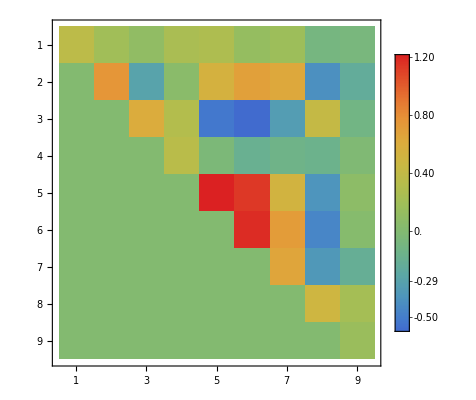

```mathematica
upperW=UpperTriangularPart[W];
MatrixForm[upperW]
MatrixPlot[upperW,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameTicks->Automatic]
```

Can we redo everything with just 6 nullifiers? Maybe! 

To recover a valid SOS certificate, our set of nullifiers must satisfy:
	1.	Span Condition: The span of the monomials in the nullifiers must be large enough to express the Bell operator and its algebraic structure (i.e., we must be able to expand 1 - β in the basis N^+WN).
	2.	Closure under the algebra: The products N_k^+N_l must cover all monomials appearing in β. If they don’t,  we’re missing key components and no matrix W in the smaller basis will suffice.

## Reducing the dimension

Now, we want to reduce the dimension of the problem. We have a good basis of nullifiers, but it can get better. We can remove some redundancy and get easier nullifiers. Since we are working at the right level of the hierarchy, it should be fine. First, we develop  a tool to speedup the calculations:

### Compute the change of basis matrix for the general case

```mathematica
MonomialBasis={II,A[0],A[1],B[0],B[1],A[0].B[0],A[0].B[1],A[1].B[0],A[1].B[1],A[0].B[0].B[1],A[0].B[1].B[0],A[1].B[0].B[1],A[1].B[1].B[0]};
exprToVector[expr_,basis_]:=Table[Coefficient[expr,basis[[j]]],{j,Length[basis]}];
```

```mathematica
U=Map[exprToVector[#,MonomialBasis]&,Nullbasis2];
U//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-√2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0
-√2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -√2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

### 7 Nullifiers

```mathematica
Nullbasis7 = {nc[A0]-nc[A1,B1,B0],nc[A1]+(nc[B1]-nc[B0])/(√2),nc[A0,B0]+nc[A1,B1],nc[A0,B1]-nc[A1,B0],nc[Id]-(nc[A0,B1]+nc[A1,B1])/(√2),nc[A1,B0,B1]-nc[A1,B1,B0],nc[A0,B0,B1]+nc[A0,B1,B0]};
Nullbasis7//MatrixForm
```

(nc[A0]-nc[A1,B1,B0]
nc[A1]+(-nc[B0]+nc[B1])/(√2)
nc[A0,B0]+nc[A1,B1]
nc[A0,B1]-nc[A1,B0]
nc[Id]-(nc[A0,B1]+nc[A1,B1])/(√2)
nc[A1,B0,B1]-nc[A1,B1,B0]
nc[A0,B0,B1]+nc[A0,B1,B0])

```mathematica
MonomialBasisnc={nc[Id], nc[A0],nc[A1],nc[B0],nc[B1],nc[A0,B0],nc[A0,B1],nc[A1,B0],nc[A1,B1],nc[A0,B0,B1],nc[A0,B1,B0],nc[A1,B0,B1],nc[A1,B1,B0]};
```

```mathematica
U=Map[exprToVector[#,MonomialBasisnc]&,Nullbasis7];
U//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0)

```mathematica
Nullbasis6 = {nc[A0]-nc[A1,B1,B0],nc[A1]+(nc[B1]-nc[B0])/(√2),nc[A0,B0]+nc[A1,B1],nc[A0,B1]-nc[A1,B0],nc[Id]-(nc[A0,B1]+nc[A1,B1])/(√2),nc[A1,B0,B1]-nc[A1,B1,B0]};
Nullbasis6//MatrixForm
```

(nc[A0]-nc[A1,B1,B0]
nc[A1]+(-nc[B0]+nc[B1])/(√2)
nc[A0,B0]+nc[A1,B1]
nc[A0,B1]-nc[A1,B0]
nc[Id]-(nc[A0,B1]+nc[A1,B1])/(√2)
nc[A1,B0,B1]-nc[A1,B1,B0])

```mathematica
U6=Map[exprToVector[#,MonomialBasisnc]&,Nullbasis6];
U6//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

```mathematica
W6 = U6.Γ.ConjugateTranspose[U6];
W6 //MatrixForm
```

(0.12205128520670647 | 0.0403144991261158391 | 0.0558415644332638508 | 0.0506397750170026815 | -0.0722350855148858574 | 0.0565953970250852138
0.0403144991261158391 | 0.349624295600633711 | 0.0631895264224206878 | -0.0631895103356776255 | -0.0006513135659807787 | 1.512382792×10^-9
0.0558415644332638508 | 0.0631895264224206878 | 0.119849747010545427 | 0.036575078186265753 | -0.070765117482659361 | 0.0565812637185866482
0.0506397750170026815 | -0.0631895103356776255 | 0.036575078186265753 | 0.119849740093233814 | -0.071218736783000504 | 0.0565812544133858105
-0.0722350855148858574 | -0.0006513135659807787 | -0.070765117482659361 | -0.071218736783000504 | 0.319411363801946823 | 0.026980239924077634
0.0565953970250852138 | 1.512382792×10^-9 | 0.0565812637185866482 | 0.0565812544133858105 | 0.026980239924077634 | 0.0736894015525673893)

Since W is symmetric:

```mathematica
upperW6=UpperTriangularPart[W6];
MatrixForm[upperW6]
```

(0.12205128520670647 | 0.0403144991261158391 | 0.0558415644332638508 | 0.0506397750170026815 | -0.0722350855148858574 | 0.0565953970250852138
0 | 0.349624295600633711 | 0.0631895264224206878 | -0.0631895103356776255 | -0.0006513135659807787 | 1.512382792×10^-9
0 | 0 | 0.119849747010545427 | 0.036575078186265753 | -0.070765117482659361 | 0.0565812637185866482
0 | 0 | 0 | 0.119849740093233814 | -0.071218736783000504 | 0.0565812544133858105
0 | 0 | 0 | 0 | 0.319411363801946823 | 0.026980239924077634
0 | 0 | 0 | 0 | 0 | 0.0736894015525673893)

There is indeed some structure... 
- w33 = w44,
- w26 = 0,
- w16 = w36 = w46,
- w23 = - w24,

In the end, we got rid of 5 variables... not bad.

## SOS decomposition of the Bell expression

### Bell expression

We express our Bell expression in terms of non-commuting variables

```mathematica
β[p1_,p4_]:=1/16 (4 (4 p1 nc[A0]+8 p4 nc[A1]+√2 (nc[B0]+nc[B1]) Cot[2θ] Csc[2θ])+1/(√2)Csc[θ]^2 Sec[θ]^2 (p1 (nc[B0]+nc[B1]) (-3+Cos[4θ])-2 (-p1 Cos[2θ]+Cos[4θ]) nc[A0,B0]-2 (-p1 Cos[2θ]+Cos[4θ]) nc[A0,B1]+2 Sin[2 θ] (4 p4 (-nc[B0]+nc[B1]) Sin[2 θ]^2+nc[A1,B1] (-1+p1 Cos[2θ]-2p4 Sin[4θ])-nc[A1,B0] (-1+p1 Cos[2 θ]+2 p4 Sin[4θ]))));
```

Now, consider vertex number 7. The coordinates of the vertex are given by

```mathematica
v7={(2 √2+√2 Csc[2 θ]^2-2 Csc[θ] Sec[θ])/(2 √2+Cot[2 θ] (-2+√2 Csc[2 θ])-Csc[θ] Sec[θ]),0};
```

For θ = π/4, we have

```mathematica
β[p1,p4]/.θ->π/4//Simplify
```

p1 nc[A0]+2 p4 nc[A1]+(-2 (p1+2 p4) nc[B0]-2 (p1-2 p4) nc[B1]+nc[A0,B0]+nc[A0,B1]+nc[A1,B0]-nc[A1,B1])/(2 √2)

```mathematica
beta = β[v7[[1]],v7[[2]]]/.θ->π/4//FullSimplify
```

(1-1/(√2)) nc[A0]+((-2+√2) nc[B0]+(-2+√2) nc[B1]+nc[A0,B0]+nc[A0,B1]+nc[A1,B0]-nc[A1,B1])/(2 √2)

### Certificate

Given the following basis of nullifiers:

```mathematica
Nullbasis6//MatrixForm
```

(nc[A0]-nc[A1,B1,B0]
nc[A1]+(-nc[B0]+nc[B1])/(√2)
nc[A0,B0]+nc[A1,B1]
nc[A0,B1]-nc[A1,B0]
nc[Id]-(nc[A0,B1]+nc[A1,B1])/(√2)
nc[A1,B0,B1]-nc[A1,B1,B0])

We want to find a certificate G

```mathematica
n=Length[Nullbasis6];
G=Table[If[i<=j,g[i,j],g[j,i]],{i,n},{j,n}];
G //MatrixForm
SymmetricMatrixQ[G]
```

(g[1,1] | g[1,2] | g[1,3] | g[1,4] | g[1,5] | g[1,6]
g[1,2] | g[2,2] | g[2,3] | g[2,4] | g[2,5] | g[2,6]
g[1,3] | g[2,3] | g[3,3] | g[3,4] | g[3,5] | g[3,6]
g[1,4] | g[2,4] | g[3,4] | g[4,4] | g[4,5] | g[4,6]
g[1,5] | g[2,5] | g[3,5] | g[4,5] | g[5,5] | g[5,6]
g[1,6] | g[2,6] | g[3,6] | g[4,6] | g[5,6] | g[6,6])

True

The SOS decomposition should read

```mathematica
expr=simplify[ncDot[Nullbasis6,G,Nullbasis6]];
```

```mathematica
expr2=Expand[nc[Id]-beta-expr]//simplify;
```

Then, for each monomial, the coefficients are

```mathematica
expr2
```

nc[]-g[1,1] nc[]+2 g[1,6] nc[]-2 g[2,2] nc[]-2 g[3,3] nc[]+√2 g[3,5] nc[]-2 g[4,4] nc[]+√2 g[4,5] nc[]-2 g[5,5] nc[]+2 g[6,6] nc[]-nc[A0]+nc[A0]/(√2)-2 g[1,5] nc[A0]+√2 g[2,3] nc[A0]-√2 g[2,4] nc[A0]+g[2,5] nc[A0]-√2 g[2,3] nc[A1]-√2 g[2,4] nc[A1]-g[2,5] nc[A1]-nc[B0]/2+nc[B0]/(√2)-g[1,3] nc[B0]-(g[1,5] nc[B0])/(√2)+2 g[2,4] nc[B0]+√2 g[2,5] nc[B0]-nc[B1]/2+nc[B1]/(√2)-3 g[1,4] nc[B1]+√2 g[1,5] nc[B1]-2 g[2,3] nc[B1]-g[1,2] nc[A0,A1]+(g[3,5] nc[A0,A1])/(√2)+(g[4,5] nc[A0,A1])/(√2)-1/2 g[5,5] nc[A0,A1]-g[1,2] nc[A1,A0]+(g[3,5] nc[A1,A0])/(√2)+(g[4,5] nc[A1,A0])/(√2)-1/2 g[5,5] nc[A1,A0]-nc[B0,A0]/(2 √2)+√2 g[1,2] nc[B0,A0]-2 g[3,5] nc[B0,A0]-nc[B0,A1]/(2 √2)+(g[1,2] nc[B0,A1])/(√2)+√2 g[2,2] nc[B0,A1]+2 g[4,5] nc[B0,A1]+1/2 g[2,2] nc[B0,B1]-2 g[2,6] nc[B0,B1]+(g[3,5] nc[B0,B1])/(√2)-(g[4,5] nc[B0,B1])/(√2)-nc[B1,A0]/(2 √2)-√2 g[1,2] nc[B1,A0]-2 g[4,5] nc[B1,A0]+√2 g[5,5] nc[B1,A0]+nc[B1,A1]/(2 √2)-(g[1,2] nc[B1,A1])/(√2)-√2 g[2,2] nc[B1,A1]-2 g[3,5] nc[B1,A1]+√2 g[5,5] nc[B1,A1]+2 g[1,2] nc[B1,B0]+1/2 g[2,2] nc[B1,B0]+2 g[2,6] nc[B1,B0]+(g[3,5] nc[B1,B0])/(√2)-(g[4,5] nc[B1,B0])/(√2)+2 g[1,4] nc[B0,A0,A1]-(g[1,5] nc[B0,A0,A1])/(√2)-g[2,3] nc[B0,A0,A1]+g[4,6] nc[B0,A0,A1]-(g[5,6] nc[B0,A0,A1])/(√2)+g[1,4] nc[B0,A1,A0]-g[2,3] nc[B0,A1,A0]-g[4,6] nc[B0,A1,A0]+(g[5,6] nc[B0,A1,A0])/(√2)-(g[2,3] nc[B0,B1,A0])/(√2)+(g[2,4] nc[B0,B1,A0])/(√2)-1/2 g[2,5] nc[B0,B1,A0]+(g[2,3] nc[B0,B1,A1])/(√2)+(g[2,4] nc[B0,B1,A1])/(√2)-1/2 g[2,5] nc[B0,B1,A1]-2 g[5,6] nc[B0,B1,A1]-g[1,4] nc[B0,B1,B0]-g[1,3] nc[B1,A0,A1]+(g[1,5] nc[B1,A0,A1])/(√2)-g[2,4] nc[B1,A0,A1]+(g[2,5] nc[B1,A0,A1])/(√2)-g[3,6] nc[B1,A0,A1]+(g[1,5] nc[B1,A1,A0])/(√2)-g[2,4] nc[B1,A1,A0]+(g[2,5] nc[B1,A1,A0])/(√2)+g[3,6] nc[B1,A1,A0]-(g[2,3] nc[B1,B0,A0])/(√2)+(g[2,4] nc[B1,B0,A0])/(√2)-1/2 g[2,5] nc[B1,B0,A0]+2 g[1,5] nc[B1,B0,A1]+(g[2,3] nc[B1,B0,A1])/(√2)+(g[2,4] nc[B1,B0,A1])/(√2)-1/2 g[2,5] nc[B1,B0,A1]+2 g[5,6] nc[B1,B0,A1]+g[1,3] nc[B1,B0,B1]-(g[1,5] nc[B1,B0,B1])/(√2)-g[1,6] nc[B0,B1,A0,A1]-g[3,3] nc[B0,B1,A0,A1]+(g[3,5] nc[B0,B1,A0,A1])/(√2)-g[1,6] nc[B0,B1,A1,A0]+g[4,4] nc[B0,B1,A1,A0]-(g[4,5] nc[B0,B1,A1,A0])/(√2)-(g[1,2] nc[B0,B1,B0,A1])/(√2)-g[6,6] nc[B0,B1,B0,B1]+g[1,1] nc[B1,B0,A0,A1]+g[1,6] nc[B1,B0,A0,A1]+g[4,4] nc[B1,B0,A0,A1]-(g[4,5] nc[B1,B0,A0,A1])/(√2)+g[1,1] nc[B1,B0,A1,A0]+g[1,6] nc[B1,B0,A1,A0]-g[3,3] nc[B1,B0,A1,A0]+(g[3,5] nc[B1,B0,A1,A0])/(√2)+(g[1,2] nc[B1,B0,B1,A1])/(√2)-g[1,1] nc[B1,B0,B1,B0]-2 g[1,6] nc[B1,B0,B1,B0]-g[6,6] nc[B1,B0,B1,B0]+g[1,3] nc[B0,B1,B0,A0,A1]+g[3,6] nc[B0,B1,B0,A0,A1]-g[3,6] nc[B0,B1,B0,A1,A0]-g[4,6] nc[B1,B0,B1,A0,A1]+(g[5,6] nc[B1,B0,B1,A0,A1])/(√2)+g[1,4] nc[B1,B0,B1,A1,A0]-(g[1,5] nc[B1,B0,B1,A1,A0])/(√2)+g[4,6] nc[B1,B0,B1,A1,A0]-(g[5,6] nc[B1,B0,B1,A1,A0])/(√2)

```mathematica
monomials=Cases[expr2,nc[___],Infinity];
monomials=DeleteDuplicates[monomials]
```

{nc[],nc[A0],nc[A1],nc[B0],nc[B1],nc[A0,A1],nc[A1,A0],nc[B0,A0],nc[B0,A1],nc[B0,B1],nc[B1,A0],nc[B1,A1],nc[B1,B0],nc[B0,A0,A1],nc[B0,A1,A0],nc[B0,B1,A0],nc[B0,B1,A1],nc[B0,B1,B0],nc[B1,A0,A1],nc[B1,A1,A0],nc[B1,B0,A0],nc[B1,B0,A1],nc[B1,B0,B1],nc[B0,B1,A0,A1],nc[B0,B1,A1,A0],nc[B0,B1,B0,A1],nc[B0,B1,B0,B1],nc[B1,B0,A0,A1],nc[B1,B0,A1,A0],nc[B1,B0,B1,A1],nc[B1,B0,B1,B0],nc[B0,B1,B0,A0,A1],nc[B0,B1,B0,A1,A0],nc[B1,B0,B1,A0,A1],nc[B1,B0,B1,A1,A0]}

```mathematica
Length[monomials]
```

35

```mathematica
coefficients=Table[Coefficient[expr2,monomial],{monomial,monomials}];
```

```mathematica
coefficients
```

{1-g[1,1]+2 g[1,6]-2 g[2,2]-2 g[3,3]+√2 g[3,5]-2 g[4,4]+√2 g[4,5]-2 g[5,5]+2 g[6,6],-1+1/(√2)-2 g[1,5]+√2 g[2,3]-√2 g[2,4]+g[2,5],-√2 g[2,3]-√2 g[2,4]-g[2,5],-1/2+1/(√2)-g[1,3]-g[1,5]/(√2)+2 g[2,4]+√2 g[2,5],-1/2+1/(√2)-3 g[1,4]+√2 g[1,5]-2 g[2,3],-g[1,2]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5],-g[1,2]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5],-1/(2 √2)+√2 g[1,2]-2 g[3,5],-1/(2 √2)+g[1,2]/(√2)+√2 g[2,2]+2 g[4,5],1/2 g[2,2]-2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2),-1/(2 √2)-√2 g[1,2]-2 g[4,5]+√2 g[5,5],1/(2 √2)-g[1,2]/(√2)-√2 g[2,2]-2 g[3,5]+√2 g[5,5],2 g[1,2]+1/2 g[2,2]+2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2),2 g[1,4]-g[1,5]/(√2)-g[2,3]+g[4,6]-g[5,6]/(√2),g[1,4]-g[2,3]-g[4,6]+g[5,6]/(√2),-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5],g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,6],-g[1,4],-g[1,3]+g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)-g[3,6],g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)+g[3,6],-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5],2 g[1,5]+g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]+2 g[5,6],g[1,3]-g[1,5]/(√2),-g[1,6]-g[3,3]+g[3,5]/(√2),-g[1,6]+g[4,4]-g[4,5]/(√2),-g[1,2]/(√2),-g[6,6],g[1,1]+g[1,6]+g[4,4]-g[4,5]/(√2),g[1,1]+g[1,6]-g[3,3]+g[3,5]/(√2),g[1,2]/(√2),-g[1,1]-2 g[1,6]-g[6,6],g[1,3]+g[3,6],-g[3,6],-g[4,6]+g[5,6]/(√2),g[1,4]-g[1,5]/(√2)+g[4,6]-g[5,6]/(√2)}

### Checks

Just to be sure, try to reconstruct the expression

```mathematica
reorganizedExpr=Total[Table[nc[monomials[[i]]]*coefficients[[i]],{i,Length[monomials]}]];
```

```mathematica
expr2-reorganizedExpr==0//Simplify
```

True

It works!

### Solutions

All the coefficients should be zero:

```mathematica
eqs=Thread[Flatten[coefficients]==0];
```

```mathematica
eqs
```

{1-g[1,1]+2 g[1,6]-2 g[2,2]-2 g[3,3]+√2 g[3,5]-2 g[4,4]+√2 g[4,5]-2 g[5,5]+2 g[6,6]==0,-1+1/(√2)-2 g[1,5]+√2 g[2,3]-√2 g[2,4]+g[2,5]==0,-√2 g[2,3]-√2 g[2,4]-g[2,5]==0,-1/2+1/(√2)-g[1,3]-g[1,5]/(√2)+2 g[2,4]+√2 g[2,5]==0,-1/2+1/(√2)-3 g[1,4]+√2 g[1,5]-2 g[2,3]==0,-g[1,2]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5]==0,-g[1,2]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5]==0,-1/(2 √2)+√2 g[1,2]-2 g[3,5]==0,-1/(2 √2)+g[1,2]/(√2)+√2 g[2,2]+2 g[4,5]==0,1/2 g[2,2]-2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2)==0,-1/(2 √2)-√2 g[1,2]-2 g[4,5]+√2 g[5,5]==0,1/(2 √2)-g[1,2]/(√2)-√2 g[2,2]-2 g[3,5]+√2 g[5,5]==0,2 g[1,2]+1/2 g[2,2]+2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2)==0,2 g[1,4]-g[1,5]/(√2)-g[2,3]+g[4,6]-g[5,6]/(√2)==0,g[1,4]-g[2,3]-g[4,6]+g[5,6]/(√2)==0,-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]==0,g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,6]==0,-g[1,4]==0,-g[1,3]+g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)-g[3,6]==0,g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)+g[3,6]==0,-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]==0,2 g[1,5]+g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]+2 g[5,6]==0,g[1,3]-g[1,5]/(√2)==0,-g[1,6]-g[3,3]+g[3,5]/(√2)==0,-g[1,6]+g[4,4]-g[4,5]/(√2)==0,-g[1,2]/(√2)==0,-g[6,6]==0,g[1,1]+g[1,6]+g[4,4]-g[4,5]/(√2)==0,g[1,1]+g[1,6]-g[3,3]+g[3,5]/(√2)==0,g[1,2]/(√2)==0,-g[1,1]-2 g[1,6]-g[6,6]==0,g[1,3]+g[3,6]==0,-g[3,6]==0,-g[4,6]+g[5,6]/(√2)==0,g[1,4]-g[1,5]/(√2)+g[4,6]-g[5,6]/(√2)==0}

```mathematica
Length[eqs]
```

35

```mathematica
Solve[eqs, DeleteDuplicates[Flatten[G]]]
```

{}

## Retry everything with 7 nullifiers

### Certificate

Given the following basis of 7 nullifiers:

```mathematica
Nullbasis7//MatrixForm
```

(nc[A0]-nc[A1,B1,B0]
nc[A1]+(-nc[B0]+nc[B1])/(√2)
nc[A0,B0]+nc[A1,B1]
nc[A0,B1]-nc[A1,B0]
nc[Id]-(nc[A0,B1]+nc[A1,B1])/(√2)
nc[A1,B0,B1]-nc[A1,B1,B0]
nc[A0,B0,B1]+nc[A0,B1,B0])

We want to find a certificate G

```mathematica
n=Length[Nullbasis7];
G=Table[If[i<=j,g[i,j],g[j,i]],{i,n},{j,n}];
G //MatrixForm
SymmetricMatrixQ[G]
```

(g[1,1] | g[1,2] | g[1,3] | g[1,4] | g[1,5] | g[1,6] | g[1,7]
g[1,2] | g[2,2] | g[2,3] | g[2,4] | g[2,5] | g[2,6] | g[2,7]
g[1,3] | g[2,3] | g[3,3] | g[3,4] | g[3,5] | g[3,6] | g[3,7]
g[1,4] | g[2,4] | g[3,4] | g[4,4] | g[4,5] | g[4,6] | g[4,7]
g[1,5] | g[2,5] | g[3,5] | g[4,5] | g[5,5] | g[5,6] | g[5,7]
g[1,6] | g[2,6] | g[3,6] | g[4,6] | g[5,6] | g[6,6] | g[6,7]
g[1,7] | g[2,7] | g[3,7] | g[4,7] | g[5,7] | g[6,7] | g[7,7])

True

The SOS decomposition should read

```mathematica
expr=simplify[ncDot[Nullbasis7,G,Nullbasis7]];
```

```mathematica
expr2=Expand[nc[Id]-beta-expr]//simplify;
```

Then, for each monomial, the coefficients are

```mathematica
expr2
```

nc[]-g[1,1] nc[]+2 g[1,6] nc[]-2 g[2,2] nc[]-2 g[3,3] nc[]+√2 g[3,5] nc[]-2 g[4,4] nc[]+√2 g[4,5] nc[]-2 g[5,5] nc[]+2 g[6,6] nc[]-2 g[7,7] nc[]-nc[A0]+nc[A0]/(√2)-2 g[1,5] nc[A0]+√2 g[2,3] nc[A0]-√2 g[2,4] nc[A0]+g[2,5] nc[A0]-√2 g[2,3] nc[A1]-√2 g[2,4] nc[A1]-g[2,5] nc[A1]-nc[B0]/2+nc[B0]/(√2)-g[1,3] nc[B0]-(g[1,5] nc[B0])/(√2)+2 g[2,4] nc[B0]+√2 g[2,5] nc[B0]-2 g[4,7] nc[B0]+√2 g[5,7] nc[B0]-nc[B1]/2+nc[B1]/(√2)-3 g[1,4] nc[B1]+√2 g[1,5] nc[B1]-2 g[2,3] nc[B1]-2 g[3,7] nc[B1]-g[1,2] nc[A0,A1]+g[1,7] nc[A0,A1]+(g[3,5] nc[A0,A1])/(√2)+(g[4,5] nc[A0,A1])/(√2)-1/2 g[5,5] nc[A0,A1]-g[1,2] nc[A1,A0]+g[1,7] nc[A1,A0]+(g[3,5] nc[A1,A0])/(√2)+(g[4,5] nc[A1,A0])/(√2)-1/2 g[5,5] nc[A1,A0]-nc[B0,A0]/(2 √2)+√2 g[1,2] nc[B0,A0]-√2 g[2,7] nc[B0,A0]-2 g[3,5] nc[B0,A0]-nc[B0,A1]/(2 √2)+(g[1,2] nc[B0,A1])/(√2)+√2 g[2,2] nc[B0,A1]+2 g[4,5] nc[B0,A1]-2 g[1,7] nc[B0,B1]+1/2 g[2,2] nc[B0,B1]-2 g[2,6] nc[B0,B1]+(g[3,5] nc[B0,B1])/(√2)-(g[4,5] nc[B0,B1])/(√2)-nc[B1,A0]/(2 √2)-√2 g[1,2] nc[B1,A0]+√2 g[2,7] nc[B1,A0]-2 g[4,5] nc[B1,A0]+√2 g[5,5] nc[B1,A0]+nc[B1,A1]/(2 √2)-(g[1,2] nc[B1,A1])/(√2)-√2 g[2,2] nc[B1,A1]-2 g[3,5] nc[B1,A1]+√2 g[5,5] nc[B1,A1]+2 g[1,2] nc[B1,B0]-2 g[1,7] nc[B1,B0]+1/2 g[2,2] nc[B1,B0]+2 g[2,6] nc[B1,B0]+(g[3,5] nc[B1,B0])/(√2)-(g[4,5] nc[B1,B0])/(√2)+2 g[1,4] nc[B0,A0,A1]-(g[1,5] nc[B0,A0,A1])/(√2)-g[2,3] nc[B0,A0,A1]-g[3,7] nc[B0,A0,A1]+g[4,6] nc[B0,A0,A1]-(g[5,6] nc[B0,A0,A1])/(√2)+(g[5,7] nc[B0,A0,A1])/(√2)+g[1,4] nc[B0,A1,A0]-g[2,3] nc[B0,A1,A0]-g[3,7] nc[B0,A1,A0]-g[4,6] nc[B0,A1,A0]+(g[5,6] nc[B0,A1,A0])/(√2)+(g[5,7] nc[B0,A1,A0])/(√2)-(g[2,3] nc[B0,B1,A0])/(√2)+(g[2,4] nc[B0,B1,A0])/(√2)-1/2 g[2,5] nc[B0,B1,A0]-2 g[5,7] nc[B0,B1,A0]+(g[2,3] nc[B0,B1,A1])/(√2)+(g[2,4] nc[B0,B1,A1])/(√2)-1/2 g[2,5] nc[B0,B1,A1]-2 g[5,6] nc[B0,B1,A1]-g[1,4] nc[B0,B1,B0]-2 g[3,7] nc[B0,B1,B0]-g[1,3] nc[B1,A0,A1]+(g[1,5] nc[B1,A0,A1])/(√2)-g[2,4] nc[B1,A0,A1]+(g[2,5] nc[B1,A0,A1])/(√2)-g[3,6] nc[B1,A0,A1]+g[4,7] nc[B1,A0,A1]+(g[1,5] nc[B1,A1,A0])/(√2)-g[2,4] nc[B1,A1,A0]+(g[2,5] nc[B1,A1,A0])/(√2)+g[3,6] nc[B1,A1,A0]+g[4,7] nc[B1,A1,A0]-(g[2,3] nc[B1,B0,A0])/(√2)+(g[2,4] nc[B1,B0,A0])/(√2)-1/2 g[2,5] nc[B1,B0,A0]-2 g[5,7] nc[B1,B0,A0]+2 g[1,5] nc[B1,B0,A1]+(g[2,3] nc[B1,B0,A1])/(√2)+(g[2,4] nc[B1,B0,A1])/(√2)-1/2 g[2,5] nc[B1,B0,A1]+2 g[5,6] nc[B1,B0,A1]+g[1,3] nc[B1,B0,B1]-(g[1,5] nc[B1,B0,B1])/(√2)-2 g[4,7] nc[B1,B0,B1]+√2 g[5,7] nc[B1,B0,B1]-g[1,6] nc[B0,B1,A0,A1]-g[2,7] nc[B0,B1,A0,A1]-g[3,3] nc[B0,B1,A0,A1]+(g[3,5] nc[B0,B1,A0,A1])/(√2)-g[1,6] nc[B0,B1,A1,A0]-g[2,7] nc[B0,B1,A1,A0]+g[4,4] nc[B0,B1,A1,A0]-(g[4,5] nc[B0,B1,A1,A0])/(√2)+√2 g[2,7] nc[B0,B1,B0,A0]-(g[1,2] nc[B0,B1,B0,A1])/(√2)-g[6,6] nc[B0,B1,B0,B1]-g[7,7] nc[B0,B1,B0,B1]+g[1,1] nc[B1,B0,A0,A1]+g[1,6] nc[B1,B0,A0,A1]-g[2,7] nc[B1,B0,A0,A1]+g[4,4] nc[B1,B0,A0,A1]-(g[4,5] nc[B1,B0,A0,A1])/(√2)+g[1,1] nc[B1,B0,A1,A0]+g[1,6] nc[B1,B0,A1,A0]-g[2,7] nc[B1,B0,A1,A0]-g[3,3] nc[B1,B0,A1,A0]+(g[3,5] nc[B1,B0,A1,A0])/(√2)-√2 g[2,7] nc[B1,B0,B1,A0]+(g[1,2] nc[B1,B0,B1,A1])/(√2)-g[1,1] nc[B1,B0,B1,B0]-2 g[1,6] nc[B1,B0,B1,B0]-g[6,6] nc[B1,B0,B1,B0]-g[7,7] nc[B1,B0,B1,B0]+g[1,3] nc[B0,B1,B0,A0,A1]+g[3,6] nc[B0,B1,B0,A0,A1]+g[4,7] nc[B0,B1,B0,A0,A1]-g[3,6] nc[B0,B1,B0,A1,A0]+g[4,7] nc[B0,B1,B0,A1,A0]-g[3,7] nc[B1,B0,B1,A0,A1]-g[4,6] nc[B1,B0,B1,A0,A1]+(g[5,6] nc[B1,B0,B1,A0,A1])/(√2)+(g[5,7] nc[B1,B0,B1,A0,A1])/(√2)+g[1,4] nc[B1,B0,B1,A1,A0]-(g[1,5] nc[B1,B0,B1,A1,A0])/(√2)-g[3,7] nc[B1,B0,B1,A1,A0]+g[4,6] nc[B1,B0,B1,A1,A0]-(g[5,6] nc[B1,B0,B1,A1,A0])/(√2)+(g[5,7] nc[B1,B0,B1,A1,A0])/(√2)-g[6,7] nc[B0,B1,B0,B1,A0,A1]-g[6,7] nc[B0,B1,B0,B1,A1,A0]+g[1,7] nc[B1,B0,B1,B0,A0,A1]+g[6,7] nc[B1,B0,B1,B0,A0,A1]+g[1,7] nc[B1,B0,B1,B0,A1,A0]+g[6,7] nc[B1,B0,B1,B0,A1,A0]

```mathematica
monomials=Cases[expr2,nc[___],Infinity];
monomials=DeleteDuplicates[monomials]
```

{nc[],nc[A0],nc[A1],nc[B0],nc[B1],nc[A0,A1],nc[A1,A0],nc[B0,A0],nc[B0,A1],nc[B0,B1],nc[B1,A0],nc[B1,A1],nc[B1,B0],nc[B0,A0,A1],nc[B0,A1,A0],nc[B0,B1,A0],nc[B0,B1,A1],nc[B0,B1,B0],nc[B1,A0,A1],nc[B1,A1,A0],nc[B1,B0,A0],nc[B1,B0,A1],nc[B1,B0,B1],nc[B0,B1,A0,A1],nc[B0,B1,A1,A0],nc[B0,B1,B0,A0],nc[B0,B1,B0,A1],nc[B0,B1,B0,B1],nc[B1,B0,A0,A1],nc[B1,B0,A1,A0],nc[B1,B0,B1,A0],nc[B1,B0,B1,A1],nc[B1,B0,B1,B0],nc[B0,B1,B0,A0,A1],nc[B0,B1,B0,A1,A0],nc[B1,B0,B1,A0,A1],nc[B1,B0,B1,A1,A0],nc[B0,B1,B0,B1,A0,A1],nc[B0,B1,B0,B1,A1,A0],nc[B1,B0,B1,B0,A0,A1],nc[B1,B0,B1,B0,A1,A0]}

```mathematica
Length[monomials]
```

41

```mathematica
coefficients=Table[Coefficient[expr2,monomial],{monomial,monomials}];
```

```mathematica
coefficients
```

{1-g[1,1]+2 g[1,6]-2 g[2,2]-2 g[3,3]+√2 g[3,5]-2 g[4,4]+√2 g[4,5]-2 g[5,5]+2 g[6,6]-2 g[7,7],-1+1/(√2)-2 g[1,5]+√2 g[2,3]-√2 g[2,4]+g[2,5],-√2 g[2,3]-√2 g[2,4]-g[2,5],-1/2+1/(√2)-g[1,3]-g[1,5]/(√2)+2 g[2,4]+√2 g[2,5]-2 g[4,7]+√2 g[5,7],-1/2+1/(√2)-3 g[1,4]+√2 g[1,5]-2 g[2,3]-2 g[3,7],-g[1,2]+g[1,7]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5],-g[1,2]+g[1,7]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5],-1/(2 √2)+√2 g[1,2]-√2 g[2,7]-2 g[3,5],-1/(2 √2)+g[1,2]/(√2)+√2 g[2,2]+2 g[4,5],-2 g[1,7]+1/2 g[2,2]-2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2),-1/(2 √2)-√2 g[1,2]+√2 g[2,7]-2 g[4,5]+√2 g[5,5],1/(2 √2)-g[1,2]/(√2)-√2 g[2,2]-2 g[3,5]+√2 g[5,5],2 g[1,2]-2 g[1,7]+1/2 g[2,2]+2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2),2 g[1,4]-g[1,5]/(√2)-g[2,3]-g[3,7]+g[4,6]-g[5,6]/(√2)+g[5,7]/(√2),g[1,4]-g[2,3]-g[3,7]-g[4,6]+g[5,6]/(√2)+g[5,7]/(√2),-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,7],g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,6],-g[1,4]-2 g[3,7],-g[1,3]+g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)-g[3,6]+g[4,7],g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)+g[3,6]+g[4,7],-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,7],2 g[1,5]+g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]+2 g[5,6],g[1,3]-g[1,5]/(√2)-2 g[4,7]+√2 g[5,7],-g[1,6]-g[2,7]-g[3,3]+g[3,5]/(√2),-g[1,6]-g[2,7]+g[4,4]-g[4,5]/(√2),√2 g[2,7],-g[1,2]/(√2),-g[6,6]-g[7,7],g[1,1]+g[1,6]-g[2,7]+g[4,4]-g[4,5]/(√2),g[1,1]+g[1,6]-g[2,7]-g[3,3]+g[3,5]/(√2),-√2 g[2,7],g[1,2]/(√2),-g[1,1]-2 g[1,6]-g[6,6]-g[7,7],g[1,3]+g[3,6]+g[4,7],-g[3,6]+g[4,7],-g[3,7]-g[4,6]+g[5,6]/(√2)+g[5,7]/(√2),g[1,4]-g[1,5]/(√2)-g[3,7]+g[4,6]-g[5,6]/(√2)+g[5,7]/(√2),-g[6,7],-g[6,7],g[1,7]+g[6,7],g[1,7]+g[6,7]}

### Checks

Just to be sure, try to reconstruct the expression

```mathematica
reorganizedExpr=Total[Table[nc[monomials[[i]]]*coefficients[[i]],{i,Length[monomials]}]];
```

```mathematica
expr2-reorganizedExpr==0//Simplify
```

True

It works!

### Solutions

All the coefficients should be zero:

```mathematica
eqs=Thread[Flatten[coefficients]==0];
```

```mathematica
eqs
```

{1-g[1,1]+2 g[1,6]-2 g[2,2]-2 g[3,3]+√2 g[3,5]-2 g[4,4]+√2 g[4,5]-2 g[5,5]+2 g[6,6]-2 g[7,7]==0,-1+1/(√2)-2 g[1,5]+√2 g[2,3]-√2 g[2,4]+g[2,5]==0,-√2 g[2,3]-√2 g[2,4]-g[2,5]==0,-1/2+1/(√2)-g[1,3]-g[1,5]/(√2)+2 g[2,4]+√2 g[2,5]-2 g[4,7]+√2 g[5,7]==0,-1/2+1/(√2)-3 g[1,4]+√2 g[1,5]-2 g[2,3]-2 g[3,7]==0,-g[1,2]+g[1,7]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5]==0,-g[1,2]+g[1,7]+g[3,5]/(√2)+g[4,5]/(√2)-1/2 g[5,5]==0,-1/(2 √2)+√2 g[1,2]-√2 g[2,7]-2 g[3,5]==0,-1/(2 √2)+g[1,2]/(√2)+√2 g[2,2]+2 g[4,5]==0,-2 g[1,7]+1/2 g[2,2]-2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2)==0,-1/(2 √2)-√2 g[1,2]+√2 g[2,7]-2 g[4,5]+√2 g[5,5]==0,1/(2 √2)-g[1,2]/(√2)-√2 g[2,2]-2 g[3,5]+√2 g[5,5]==0,2 g[1,2]-2 g[1,7]+1/2 g[2,2]+2 g[2,6]+g[3,5]/(√2)-g[4,5]/(√2)==0,2 g[1,4]-g[1,5]/(√2)-g[2,3]-g[3,7]+g[4,6]-g[5,6]/(√2)+g[5,7]/(√2)==0,g[1,4]-g[2,3]-g[3,7]-g[4,6]+g[5,6]/(√2)+g[5,7]/(√2)==0,-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,7]==0,g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,6]==0,-g[1,4]-2 g[3,7]==0,-g[1,3]+g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)-g[3,6]+g[4,7]==0,g[1,5]/(√2)-g[2,4]+g[2,5]/(√2)+g[3,6]+g[4,7]==0,-g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]-2 g[5,7]==0,2 g[1,5]+g[2,3]/(√2)+g[2,4]/(√2)-1/2 g[2,5]+2 g[5,6]==0,g[1,3]-g[1,5]/(√2)-2 g[4,7]+√2 g[5,7]==0,-g[1,6]-g[2,7]-g[3,3]+g[3,5]/(√2)==0,-g[1,6]-g[2,7]+g[4,4]-g[4,5]/(√2)==0,√2 g[2,7]==0,-g[1,2]/(√2)==0,-g[6,6]-g[7,7]==0,g[1,1]+g[1,6]-g[2,7]+g[4,4]-g[4,5]/(√2)==0,g[1,1]+g[1,6]-g[2,7]-g[3,3]+g[3,5]/(√2)==0,-√2 g[2,7]==0,g[1,2]/(√2)==0,-g[1,1]-2 g[1,6]-g[6,6]-g[7,7]==0,g[1,3]+g[3,6]+g[4,7]==0,-g[3,6]+g[4,7]==0,-g[3,7]-g[4,6]+g[5,6]/(√2)+g[5,7]/(√2)==0,g[1,4]-g[1,5]/(√2)-g[3,7]+g[4,6]-g[5,6]/(√2)+g[5,7]/(√2)==0,-g[6,7]==0,-g[6,7]==0,g[1,7]+g[6,7]==0,g[1,7]+g[6,7]==0}

```mathematica
Length[eqs]
```

41

```mathematica
Solve[eqs, DeleteDuplicates[Flatten[G]]]
```

{}

## Checks

To check that it’s not a problem of the code, one should try to recover Victor’s result.

```mathematica
NN= {(nc[A0]+nc[A1])/Sqrt[2]-nc[B0], (nc[A0]-nc[A1])/Sqrt[2]-nc[B1],1-(nc[A0,B0]+nc[A1,B0])/Sqrt[2],1-(nc[A0,B1]-nc[A1,B1])/Sqrt[2],(nc[A0,B1]+nc[A1,B1])/Sqrt[2]+(nc[A0,B0]-nc[A1,B0])/Sqrt[2],nc[B1,B0]-(nc[B1,A0,B0]+nc[B1,A1,B0])/Sqrt[2],nc[B0,B1]-(nc[B0,A0,B1]-nc[B0,A1,B1])/Sqrt[2],nc[B1]+(nc[A0,B0,B1]+nc[A1,B0,B1])/Sqrt[2],nc[B0]+(nc[A0,B1,B0]-nc[A1,B1,B0])/Sqrt[2]};
NN//MatrixForm//ExpandAll
```

(nc[A0]/(√2)+nc[A1]/(√2)-nc[B0]
nc[A0]/(√2)-nc[A1]/(√2)-nc[B1]
1-nc[A0,B0]/(√2)-nc[A1,B0]/(√2)
1-nc[A0,B1]/(√2)+nc[A1,B1]/(√2)
nc[A0,B0]/(√2)+nc[A0,B1]/(√2)-nc[A1,B0]/(√2)+nc[A1,B1]/(√2)
nc[B1,B0]-nc[B1,A0,B0]/(√2)-nc[B1,A1,B0]/(√2)
nc[B0,B1]-nc[B0,A0,B1]/(√2)+nc[B0,A1,B1]/(√2)
nc[B1]+nc[A0,B0,B1]/(√2)+nc[A1,B0,B1]/(√2)
nc[B0]+nc[A0,B1,B0]/(√2)-nc[A1,B1,B0]/(√2))

### Certificate

Given the following basis of 6 nullifiers:

```mathematica
NNfinal = {NN[[1]],NN[[3]],NN[[7]],NN[[2]],NN[[6]],NN[[5]]};
NNfinal//MatrixForm
```

((nc[A0]+nc[A1])/(√2)-nc[B0]
1-(nc[A0,B0]+nc[A1,B0])/(√2)
nc[B0,B1]-(nc[B0,A0,B1]-nc[B0,A1,B1])/(√2)
(nc[A0]-nc[A1])/(√2)-nc[B1]
nc[B1,B0]-(nc[B1,A0,B0]+nc[B1,A1,B0])/(√2)
(nc[A0,B0]-nc[A1,B0])/(√2)+(nc[A0,B1]+nc[A1,B1])/(√2))

We want to find a certificate G

```mathematica
n=Length[NNfinal];
G=Table[If[i<=j,g[i,j],g[j,i]],{i,n},{j,n}];
G //MatrixForm
SymmetricMatrixQ[G]
```

(g[1,1] | g[1,2] | g[1,3] | g[1,4] | g[1,5] | g[1,6]
g[1,2] | g[2,2] | g[2,3] | g[2,4] | g[2,5] | g[2,6]
g[1,3] | g[2,3] | g[3,3] | g[3,4] | g[3,5] | g[3,6]
g[1,4] | g[2,4] | g[3,4] | g[4,4] | g[4,5] | g[4,6]
g[1,5] | g[2,5] | g[3,5] | g[4,5] | g[5,5] | g[5,6]
g[1,6] | g[2,6] | g[3,6] | g[4,6] | g[5,6] | g[6,6])

True

The Bell expression is

```mathematica
beta=(1-1/Sqrt[2])*((nc[A0]+nc[A1])/Sqrt[2]-nc[B0])+(1/(2 Sqrt[2]))*(nc[A0,B0]+nc[A1,B0]+nc[A0,B1]-nc[A1,B1] );
```

The SOS decomposition should read

```mathematica
expr=simplify[ncDot[NNfinal,G,NNfinal]];
```

```mathematica
expr2=Expand[nc[Id]-beta-expr]//simplify;
```

Then, for each monomial, the coefficients are

```mathematica
expr2
```

nc[]-2 g[1,1] nc[]-2 g[2,2] nc[]-2 g[3,5] nc[]-2 g[4,4] nc[]-2 g[6,6] nc[]+nc[A0]/2-nc[A0]/(√2)-2 √2 g[1,2] nc[A0]+√2 g[1,6] nc[A0]-√2 g[2,4] nc[A0]+2 √2 g[3,5] nc[A0]+√2 g[4,6] nc[A0]+nc[A1]/2-nc[A1]/(√2)-2 √2 g[1,2] nc[A1]-√2 g[1,6] nc[A1]+√2 g[2,4] nc[A1]+√2 g[4,6] nc[A1]+nc[B0]-nc[B0]/(√2)+4 g[1,2] nc[B0]+g[3,4] nc[B0]+g[4,5] nc[B0]-2 g[4,6] nc[B0]+g[5,6] nc[B0]+g[1,3] nc[B1]+g[1,5] nc[B1]-2 g[1,6] nc[B1]+2 g[2,4] nc[B1]-g[2,5] nc[B1]+g[3,6] nc[B1]-1/2 g[1,1] nc[A0,A1]-1/2 g[2,2] nc[A0,A1]+1/2 g[4,4] nc[A0,A1]-1/2 g[1,1] nc[A1,A0]-1/2 g[2,2] nc[A1,A0]+1/2 g[4,4] nc[A1,A0]-nc[B0,A0]/(2 √2)+√2 g[1,1] nc[B0,A0]+√2 g[1,4] nc[B0,A0]+√2 g[2,2] nc[B0,A0]-√2 g[2,6] nc[B0,A0]-(g[3,4] nc[B0,A0])/(√2)-(g[3,6] nc[B0,A0])/(√2)-(g[4,5] nc[B0,A0])/(√2)-(g[5,6] nc[B0,A0])/(√2)-nc[B0,A1]/(2 √2)+√2 g[1,1] nc[B0,A1]-√2 g[1,4] nc[B0,A1]+√2 g[2,2] nc[B0,A1]+√2 g[2,6] nc[B0,A1]+(g[3,4] nc[B0,A1])/(√2)-(g[3,6] nc[B0,A1])/(√2)-(g[4,5] nc[B0,A1])/(√2)-(g[5,6] nc[B0,A1])/(√2)-g[1,4] nc[B0,B1]-2 g[2,3] nc[B0,B1]+g[2,6] nc[B0,B1]+2 g[3,4] nc[B0,B1]-nc[B1,A0]/(2 √2)-(g[1,3] nc[B1,A0])/(√2)+√2 g[1,4] nc[B1,A0]-(g[1,5] nc[B1,A0])/(√2)+(g[2,3] nc[B1,A0])/(√2)+(g[2,5] nc[B1,A0])/(√2)-√2 g[2,6] nc[B1,A0]-(g[3,6] nc[B1,A0])/(√2)+√2 g[4,4] nc[B1,A0]-(g[5,6] nc[B1,A0])/(√2)+nc[B1,A1]/(2 √2)+(g[1,3] nc[B1,A1])/(√2)+√2 g[1,4] nc[B1,A1]-(g[1,5] nc[B1,A1])/(√2)+(g[2,3] nc[B1,A1])/(√2)+(g[2,5] nc[B1,A1])/(√2)-√2 g[2,6] nc[B1,A1]+(g[3,6] nc[B1,A1])/(√2)-√2 g[4,4] nc[B1,A1]+(g[5,6] nc[B1,A1])/(√2)-g[1,4] nc[B1,B0]+2 g[1,5] nc[B1,B0]-2 g[2,5] nc[B1,B0]+g[2,6] nc[B1,B0]+g[1,2] nc[B0,A0,A1]+1/2 g[3,6] nc[B0,A0,A1]+g[4,6] nc[B0,A0,A1]+1/2 g[5,6] nc[B0,A0,A1]+g[1,2] nc[B0,A1,A0]-1/2 g[3,6] nc[B0,A1,A0]+g[4,6] nc[B0,A1,A0]+1/2 g[5,6] nc[B0,A1,A0]-√2 g[1,3] nc[B0,B1,A0]+(g[1,6] nc[B0,B1,A0])/(√2)+√2 g[2,3] nc[B0,B1,A0]-(g[2,4] nc[B0,B1,A0])/(√2)-√2 g[3,4] nc[B0,B1,A0]+(g[4,6] nc[B0,B1,A0])/(√2)-√2 g[1,3] nc[B0,B1,A1]+(g[1,6] nc[B0,B1,A1])/(√2)-√2 g[2,3] nc[B0,B1,A1]-(g[2,4] nc[B0,B1,A1])/(√2)+√2 g[3,4] nc[B0,B1,A1]-(g[4,6] nc[B0,B1,A1])/(√2)+g[1,3] nc[B0,B1,B0]+g[1,5] nc[B0,B1,B0]-g[2,5] nc[B0,B1,B0]+g[3,6] nc[B0,B1,B0]-g[1,6] nc[B1,A0,A1]+1/2 g[2,3] nc[B1,A0,A1]-1/2 g[2,5] nc[B1,A0,A1]-1/2 g[3,6] nc[B1,A0,A1]-1/2 g[5,6] nc[B1,A0,A1]-g[1,6] nc[B1,A1,A0]-1/2 g[2,3] nc[B1,A1,A0]-1/2 g[2,5] nc[B1,A1,A0]-1/2 g[3,6] nc[B1,A1,A0]+1/2 g[5,6] nc[B1,A1,A0]-√2 g[1,5] nc[B1,B0,A0]+(g[1,6] nc[B1,B0,A0])/(√2)-(g[2,4] nc[B1,B0,A0])/(√2)+√2 g[2,5] nc[B1,B0,A0]-√2 g[4,5] nc[B1,B0,A0]+(g[4,6] nc[B1,B0,A0])/(√2)-√2 g[1,5] nc[B1,B0,A1]+(g[1,6] nc[B1,B0,A1])/(√2)-(g[2,4] nc[B1,B0,A1])/(√2)+√2 g[2,5] nc[B1,B0,A1]+√2 g[4,5] nc[B1,B0,A1]-(g[4,6] nc[B1,B0,A1])/(√2)+g[3,4] nc[B1,B0,B1]+g[4,5] nc[B1,B0,B1]+g[5,6] nc[B1,B0,B1]+1/2 g[2,6] nc[B0,B1,A0,A1]-g[3,4] nc[B0,B1,A0,A1]-1/2 g[6,6] nc[B0,B1,A0,A1]+1/2 g[2,6] nc[B0,B1,A1,A0]-g[3,4] nc[B0,B1,A1,A0]+1/2 g[6,6] nc[B0,B1,A1,A0]-(g[1,3] nc[B0,B1,B0,A0])/(√2)-(g[1,5] nc[B0,B1,B0,A0])/(√2)+(g[2,3] nc[B0,B1,B0,A0])/(√2)+(g[2,5] nc[B0,B1,B0,A0])/(√2)-(g[3,6] nc[B0,B1,B0,A0])/(√2)-(g[5,6] nc[B0,B1,B0,A0])/(√2)+(g[1,3] nc[B0,B1,B0,A1])/(√2)-(g[1,5] nc[B0,B1,B0,A1])/(√2)+(g[2,3] nc[B0,B1,B0,A1])/(√2)+(g[2,5] nc[B0,B1,B0,A1])/(√2)+(g[3,6] nc[B0,B1,B0,A1])/(√2)+(g[5,6] nc[B0,B1,B0,A1])/(√2)-2 g[3,3] nc[B0,B1,B0,B1]+g[1,5] nc[B1,B0,A0,A1]+1/2 g[2,6] nc[B1,B0,A0,A1]+1/2 g[6,6] nc[B1,B0,A0,A1]+g[1,5] nc[B1,B0,A1,A0]+1/2 g[2,6] nc[B1,B0,A1,A0]-1/2 g[6,6] nc[B1,B0,A1,A0]-(g[3,4] nc[B1,B0,B1,A0])/(√2)-(g[3,6] nc[B1,B0,B1,A0])/(√2)-(g[4,5] nc[B1,B0,B1,A0])/(√2)-(g[5,6] nc[B1,B0,B1,A0])/(√2)+(g[3,4] nc[B1,B0,B1,A1])/(√2)-(g[3,6] nc[B1,B0,B1,A1])/(√2)-(g[4,5] nc[B1,B0,B1,A1])/(√2)-(g[5,6] nc[B1,B0,B1,A1])/(√2)-2 g[5,5] nc[B1,B0,B1,B0]-1/2 g[2,3] nc[B0,B1,B0,A0,A1]-1/2 g[2,5] nc[B0,B1,B0,A0,A1]-1/2 g[3,6] nc[B0,B1,B0,A0,A1]+1/2 g[5,6] nc[B0,B1,B0,A0,A1]+1/2 g[2,3] nc[B0,B1,B0,A1,A0]-1/2 g[2,5] nc[B0,B1,B0,A1,A0]-1/2 g[3,6] nc[B0,B1,B0,A1,A0]-1/2 g[5,6] nc[B0,B1,B0,A1,A0]+√2 g[3,3] nc[B0,B1,B0,B1,A0]-√2 g[3,3] nc[B0,B1,B0,B1,A1]-1/2 g[3,6] nc[B1,B0,B1,A0,A1]+1/2 g[5,6] nc[B1,B0,B1,A0,A1]+1/2 g[3,6] nc[B1,B0,B1,A1,A0]+1/2 g[5,6] nc[B1,B0,B1,A1,A0]+√2 g[5,5] nc[B1,B0,B1,B0,A0]+√2 g[5,5] nc[B1,B0,B1,B0,A1]+1/2 g[3,3] nc[B0,B1,B0,B1,A0,A1]+1/2 g[3,3] nc[B0,B1,B0,B1,A1,A0]-1/2 g[5,5] nc[B1,B0,B1,B0,A0,A1]-1/2 g[5,5] nc[B1,B0,B1,B0,A1,A0]

```mathematica
monomials=Cases[expr2,nc[___],Infinity];
monomials=DeleteDuplicates[monomials]
```

{nc[],nc[A0],nc[A1],nc[B0],nc[B1],nc[A0,A1],nc[A1,A0],nc[B0,A0],nc[B0,A1],nc[B0,B1],nc[B1,A0],nc[B1,A1],nc[B1,B0],nc[B0,A0,A1],nc[B0,A1,A0],nc[B0,B1,A0],nc[B0,B1,A1],nc[B0,B1,B0],nc[B1,A0,A1],nc[B1,A1,A0],nc[B1,B0,A0],nc[B1,B0,A1],nc[B1,B0,B1],nc[B0,B1,A0,A1],nc[B0,B1,A1,A0],nc[B0,B1,B0,A0],nc[B0,B1,B0,A1],nc[B0,B1,B0,B1],nc[B1,B0,A0,A1],nc[B1,B0,A1,A0],nc[B1,B0,B1,A0],nc[B1,B0,B1,A1],nc[B1,B0,B1,B0],nc[B0,B1,B0,A0,A1],nc[B0,B1,B0,A1,A0],nc[B0,B1,B0,B1,A0],nc[B0,B1,B0,B1,A1],nc[B1,B0,B1,A0,A1],nc[B1,B0,B1,A1,A0],nc[B1,B0,B1,B0,A0],nc[B1,B0,B1,B0,A1],nc[B0,B1,B0,B1,A0,A1],nc[B0,B1,B0,B1,A1,A0],nc[B1,B0,B1,B0,A0,A1],nc[B1,B0,B1,B0,A1,A0]}

```mathematica
Length[monomials]
```

45

```mathematica
coefficients=Table[Coefficient[expr2,monomial],{monomial,monomials}];
```

```mathematica
coefficients
```

{1-2 g[1,1]-2 g[2,2]-2 g[3,5]-2 g[4,4]-2 g[6,6],1/2-1/(√2)-2 √2 g[1,2]+√2 g[1,6]-√2 g[2,4]+2 √2 g[3,5]+√2 g[4,6],1/2-1/(√2)-2 √2 g[1,2]-√2 g[1,6]+√2 g[2,4]+√2 g[4,6],1-1/(√2)+4 g[1,2]+g[3,4]+g[4,5]-2 g[4,6]+g[5,6],g[1,3]+g[1,5]-2 g[1,6]+2 g[2,4]-g[2,5]+g[3,6],-1/2 g[1,1]-1/2 g[2,2]+1/2 g[4,4],-1/2 g[1,1]-1/2 g[2,2]+1/2 g[4,4],-1/(2 √2)+√2 g[1,1]+√2 g[1,4]+√2 g[2,2]-√2 g[2,6]-g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2),-1/(2 √2)+√2 g[1,1]-√2 g[1,4]+√2 g[2,2]+√2 g[2,6]+g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2),-g[1,4]-2 g[2,3]+g[2,6]+2 g[3,4],-1/(2 √2)-g[1,3]/(√2)+√2 g[1,4]-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)-√2 g[2,6]-g[3,6]/(√2)+√2 g[4,4]-g[5,6]/(√2),1/(2 √2)+g[1,3]/(√2)+√2 g[1,4]-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)-√2 g[2,6]+g[3,6]/(√2)-√2 g[4,4]+g[5,6]/(√2),-g[1,4]+2 g[1,5]-2 g[2,5]+g[2,6],g[1,2]+1/2 g[3,6]+g[4,6]+1/2 g[5,6],g[1,2]-1/2 g[3,6]+g[4,6]+1/2 g[5,6],-√2 g[1,3]+g[1,6]/(√2)+√2 g[2,3]-g[2,4]/(√2)-√2 g[3,4]+g[4,6]/(√2),-√2 g[1,3]+g[1,6]/(√2)-√2 g[2,3]-g[2,4]/(√2)+√2 g[3,4]-g[4,6]/(√2),g[1,3]+g[1,5]-g[2,5]+g[3,6],-g[1,6]+1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]-1/2 g[5,6],-g[1,6]-1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]+1/2 g[5,6],-√2 g[1,5]+g[1,6]/(√2)-g[2,4]/(√2)+√2 g[2,5]-√2 g[4,5]+g[4,6]/(√2),-√2 g[1,5]+g[1,6]/(√2)-g[2,4]/(√2)+√2 g[2,5]+√2 g[4,5]-g[4,6]/(√2),g[3,4]+g[4,5]+g[5,6],1/2 g[2,6]-g[3,4]-1/2 g[6,6],1/2 g[2,6]-g[3,4]+1/2 g[6,6],-g[1,3]/(√2)-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)-g[3,6]/(√2)-g[5,6]/(√2),g[1,3]/(√2)-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)+g[3,6]/(√2)+g[5,6]/(√2),-2 g[3,3],g[1,5]+1/2 g[2,6]+1/2 g[6,6],g[1,5]+1/2 g[2,6]-1/2 g[6,6],-g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2),g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2),-2 g[5,5],-1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]+1/2 g[5,6],1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]-1/2 g[5,6],√2 g[3,3],-√2 g[3,3],-1/2 g[3,6]+1/2 g[5,6],1/2 g[3,6]+1/2 g[5,6],√2 g[5,5],√2 g[5,5],1/2 g[3,3],1/2 g[3,3],-1/2 g[5,5],-1/2 g[5,5]}

### Checks

Just to be sure, try to reconstruct the expression

```mathematica
reorganizedExpr=Total[Table[nc[monomials[[i]]]*coefficients[[i]],{i,Length[monomials]}]];
expr2-reorganizedExpr==0//Simplify
```

True

It works!

### Solutions

All the coefficients should be zero:

```mathematica
eqs=Thread[Flatten[coefficients]==0];
```

```mathematica
eqs
```

{1-2 g[1,1]-2 g[2,2]-2 g[3,5]-2 g[4,4]-2 g[6,6]==0,1/2-1/(√2)-2 √2 g[1,2]+√2 g[1,6]-√2 g[2,4]+2 √2 g[3,5]+√2 g[4,6]==0,1/2-1/(√2)-2 √2 g[1,2]-√2 g[1,6]+√2 g[2,4]+√2 g[4,6]==0,1-1/(√2)+4 g[1,2]+g[3,4]+g[4,5]-2 g[4,6]+g[5,6]==0,g[1,3]+g[1,5]-2 g[1,6]+2 g[2,4]-g[2,5]+g[3,6]==0,-1/2 g[1,1]-1/2 g[2,2]+1/2 g[4,4]==0,-1/2 g[1,1]-1/2 g[2,2]+1/2 g[4,4]==0,-1/(2 √2)+√2 g[1,1]+√2 g[1,4]+√2 g[2,2]-√2 g[2,6]-g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2)==0,-1/(2 √2)+√2 g[1,1]-√2 g[1,4]+√2 g[2,2]+√2 g[2,6]+g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2)==0,-g[1,4]-2 g[2,3]+g[2,6]+2 g[3,4]==0,-1/(2 √2)-g[1,3]/(√2)+√2 g[1,4]-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)-√2 g[2,6]-g[3,6]/(√2)+√2 g[4,4]-g[5,6]/(√2)==0,1/(2 √2)+g[1,3]/(√2)+√2 g[1,4]-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)-√2 g[2,6]+g[3,6]/(√2)-√2 g[4,4]+g[5,6]/(√2)==0,-g[1,4]+2 g[1,5]-2 g[2,5]+g[2,6]==0,g[1,2]+1/2 g[3,6]+g[4,6]+1/2 g[5,6]==0,g[1,2]-1/2 g[3,6]+g[4,6]+1/2 g[5,6]==0,-√2 g[1,3]+g[1,6]/(√2)+√2 g[2,3]-g[2,4]/(√2)-√2 g[3,4]+g[4,6]/(√2)==0,-√2 g[1,3]+g[1,6]/(√2)-√2 g[2,3]-g[2,4]/(√2)+√2 g[3,4]-g[4,6]/(√2)==0,g[1,3]+g[1,5]-g[2,5]+g[3,6]==0,-g[1,6]+1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]-1/2 g[5,6]==0,-g[1,6]-1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]+1/2 g[5,6]==0,-√2 g[1,5]+g[1,6]/(√2)-g[2,4]/(√2)+√2 g[2,5]-√2 g[4,5]+g[4,6]/(√2)==0,-√2 g[1,5]+g[1,6]/(√2)-g[2,4]/(√2)+√2 g[2,5]+√2 g[4,5]-g[4,6]/(√2)==0,g[3,4]+g[4,5]+g[5,6]==0,1/2 g[2,6]-g[3,4]-1/2 g[6,6]==0,1/2 g[2,6]-g[3,4]+1/2 g[6,6]==0,-g[1,3]/(√2)-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)-g[3,6]/(√2)-g[5,6]/(√2)==0,g[1,3]/(√2)-g[1,5]/(√2)+g[2,3]/(√2)+g[2,5]/(√2)+g[3,6]/(√2)+g[5,6]/(√2)==0,-2 g[3,3]==0,g[1,5]+1/2 g[2,6]+1/2 g[6,6]==0,g[1,5]+1/2 g[2,6]-1/2 g[6,6]==0,-g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2)==0,g[3,4]/(√2)-g[3,6]/(√2)-g[4,5]/(√2)-g[5,6]/(√2)==0,-2 g[5,5]==0,-1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]+1/2 g[5,6]==0,1/2 g[2,3]-1/2 g[2,5]-1/2 g[3,6]-1/2 g[5,6]==0,√2 g[3,3]==0,-√2 g[3,3]==0,-1/2 g[3,6]+1/2 g[5,6]==0,1/2 g[3,6]+1/2 g[5,6]==0,√2 g[5,5]==0,√2 g[5,5]==0,1/2 g[3,3]==0,1/2 g[3,3]==0,-1/2 g[5,5]==0,-1/2 g[5,5]==0}

```mathematica
Length[eqs]
```

45

```mathematica
Solve[eqs, DeleteDuplicates[Flatten[G]]]
```

{}